```mathematica
f[x_]:=7*Sqrt[x^2+x+1]+9*Exp[-x]*Sin[x]-1/(Log[x])^2
```

```mathematica
D[f[x],x]
```

(7 (1+2 x))/(2 √(1+x+x^2))+9 ⅇ^-x Cos[x]+2/(x Log[x]^3)-9 ⅇ^-x Sin[x]

```mathematica
D[f[x],x]/.x->Pi
```

-9 ⅇ^-π+(7 (1+2 π))/(2 √(1+π+π^2))+2/(π Log[π]^3)

```mathematica
NumberForm[N[D[f[x],x]/.x->Pi],16]
```

6.845543775312127

```mathematica
NumberForm[N[f[Pi]],16]
```

25.43895152854765

```mathematica
f[Pi]
```

7 √(1+π+π^2)-1/Log[π]^2

```mathematica
g[x_]:=(7/2)*(2x+1)/Sqrt[x^2+x+1]+9*Exp[-x]*(Cos[x]-Sin[x])+2/(x*(Log[x])^3)
```

```mathematica
NumberForm[N[f[0.5]],16]
```

9.79583720163469

```mathematica
NumberForm[N[f[0.9]],16]
```

-75.69354016098368

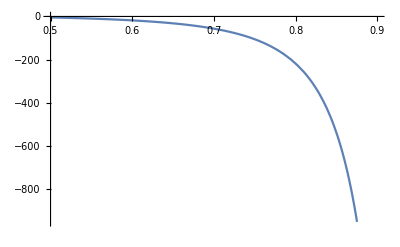

```mathematica
Plot[g[x],{x,0.5,0.9}]
```

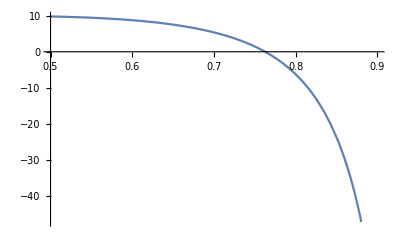

```mathematica
Plot[f[x],{x,0.5,0.9}]
```

```mathematica
NumberForm[N[g[0.9]],16]
```

-1894.639641473279